Loading The Code

```mathematica
Clear @ Evaluate[Context[]<>"*"]
SetDirectory[NotebookDirectory[]]
<< Utilities.m
<< MeltCurves.m
<< FractionBound.m
<< EvaGreen.m
```

C:\nadir\PCRModelling\MeltCurves

E16082201

#### Loading the Data

```mathematica
<< MeltCurves.m
dir = "C:\\Users\\bob\\Dropbox\\Grad School\\Lutz Lab\\FlatmerAnalysis\\";
e16082201 = loadMeltCurves[dir <> "E16082201.xlsx", 6];
e16082201["headerNames"]
data = datasetFromMeltCurves[e16082201, 
Function[{assoc}, hybridize[assoc["R16082205"] // Round, assoc["R16061005"] // Round, assoc["Well Conc (ng/uL)"]]],
Function[{header}, {
"concentration" -> header["Well Conc (ng/uL)"],
"R16082205" -> header["R16082205"],
"R16061005" -> header["R16061005"]
}]
];
```

{Well,Dilution,R16082205,R16061005,Well Conc (M),Well Conc (ng/uL)}

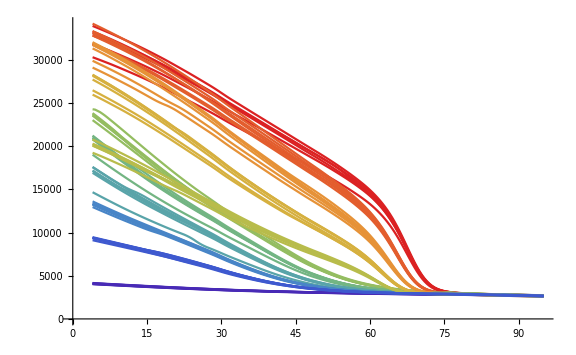

```mathematica
Get["MeltCurves`"]
plotMeltCurves[data]
```

#### Extracting Replicates

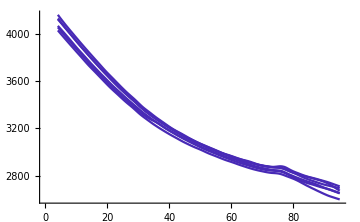

```mathematica
<< MeltCurves.m
replicates = groupMeltCurvesByReplicates[data];
blanks = hybridize[0,0,0.] /. replicates;
plotMeltCurves[blanks, ImageSize -> Medium]
```

#### Fraction Bound

{deltah→778.5,deltas→2045.5,atot→1/100000}

{Btot→Atot,Atot→1/100,t→5463/20+tau,deltaH→3.25724×10^6,deltaS→8558.37,R→8.3145}

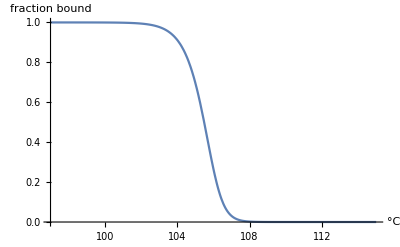

```mathematica
<< FractionBound.m
numericalUsualParameters
unitlessParameters
(* fractionBound uses usual units, not SI units *)
fb = fractionBound[τ,
deltah/.numericalUsualParameters (*kcal/mol*),
deltas/.numericalUsualParameters (*cal/(mol K)*),
atot/.numericalUsualParameters (*molar*)]//FullSimplify;
Plot[fb, {τ, 97, 115}, AxesLabel->{"°C", "fraction bound"}]
```

#### EvaGreen

```mathematica
<<EvaGreen.m
evaSignal[50, hybridize[90, 15], 200*^-9]
```

beta[50]+alpha[50] ((1/200000000000+1/80000000(-1/2500-ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))+√(ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))) √(1/1250+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))))) secondaryStructure[50,15]+1/80000000(1/2500+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))-√(ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))) √(1/1250+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500)))) (15+secondaryStructure[50,75])+(1/200000000000+1/80000000(-1/2500-ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))+√(ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))) √(1/1250+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))))) secondaryStructure[50,90])+1/sigma[50]alpha[50] ((1/200000000000+1/80000000(-1/2500-ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))+√(ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))) √(1/1250+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))))) (15-2 secondaryStructure[50,15])+1/80000000(1/2500+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))-√(ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))) √(1/1250+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500)))) (105-2 (15+secondaryStructure[50,75]))+(1/200000000000+1/80000000(-1/2500-ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))+√(ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))) √(1/1250+ⅇ^(0.00037219 (-4184 deltaH9015+(3380149 deltaS9015)/2500))))) (90-2 secondaryStructure[50,90]))